```mathematica
Clear[t,ft, v0,tp0,l,f0]
```

```mathematica
t[v0_,tp0_,l_,f0_]:=((tp-tp0)-Sqrt[(tp-tp0)^2-(1-v0^2/c^2)((tp-tp0)^2-l^2/c^2)])/(1-v0^2/c^2);
ft[v0_,tp0_,l_,f0_]:=f0/(1+v0/c(v0 t[v0,tp0,l,f0])/Sqrt[l^2+(v0 t[v0,tp0,l,f0])^2]);
```

```mathematica
FullSimplify[ft[v0,tp0,l,f0]]
```

f0/(1-(c v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4)))/((c^2-v0^2) √(l^2+(c^4 v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4))^2)/((c^2-v0^2)^2))))

```mathematica
f0/(1-(c v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4)))/((c^2-v0^2) √(l^2+(c^4 v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4))^2)/((c^2-v0^2)^2))))
```

f0/(1-(c v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4)))/((c^2-v0^2) √(l^2+(c^4 v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4))^2)/((c^2-v0^2)^2))))

```mathematica
FullSimplify[D[ft[v0,tp0,l,f0],v0]]
```

-(f0 v0 (-2 l^4 v0^4+l^2 (tp-tp0)^2 v0^6+c^6 (tp-tp0) (2 l^2+(tp-tp0)^2 v0^2) √((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4)+c^2 (4 l^4 v0^2-(tp-tp0)^4 v0^6+l^2 (tp-tp0) v0^4 (5 tp-5 tp0-3 √((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4)))-c^4 (2 l^4-3 (tp-tp0)^3 v0^4 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4))-l^2 (tp-tp0) v0^2 (-6 tp+6 tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4)))))/(c (c-v0) (c+v0) √((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4) √(l^2+(c^4 v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4))^2)/((c^2-v0^2)^2)) (c (-tp+tp0) v0^2+c v0^2 √((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4)-c^2 √(l^2+(c^4 v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4))^2)/((c^2-v0^2)^2))+v0^2 √(l^2+(c^4 v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4))^2)/((c^2-v0^2)^2)))^2)

```mathematica
FullSimplify[D[ft[v0,tp0,l,f0],f0]]
```

1/(1-(c v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4)))/((c^2-v0^2) √(l^2+(c^4 v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4))^2)/((c^2-v0^2)^2))))

```mathematica
FullSimplify[D[ft[v0,tp0,l,f0],tp0]]
```

(f0 l^2 (c-v0) v0^2 (c+v0) ((-tp+tp0) v0^2+c^2 √((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4)))/(c √((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4) √(l^2+(c^4 v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4))^2)/((c^2-v0^2)^2)) (c (-tp+tp0) v0^2+c v0^2 √((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4)-c^2 √(l^2+(c^4 v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4))^2)/((c^2-v0^2)^2))+v0^2 √(l^2+(c^4 v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4))^2)/((c^2-v0^2)^2)))^2)

```mathematica
FullSimplify[D[ft[v0,tp0,l,f0],l]]
```

(f0 l (tp-tp0) (c-v0) v0^2 (c+v0) ((-tp+tp0) v0^2+c^2 √((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4)))/(c √((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4) √(l^2+(c^4 v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4))^2)/((c^2-v0^2)^2)) (c (-tp+tp0) v0^2+c v0^2 √((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4)-c^2 √(l^2+(c^4 v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4))^2)/((c^2-v0^2)^2))+v0^2 √(l^2+(c^4 v0^2 (-tp+tp0+√((-l^2 v0^2+c^2 (l^2+(tp-tp0)^2 v0^2))/c^4))^2)/((c^2-v0^2)^2)))^2)

```mathematica
c = 343;
v0 = 50;
tp0= 115;
l = 1000;
f0 = 100;
Plot[ft[v0,tp0,l,f0],{tp,0,240}]
```

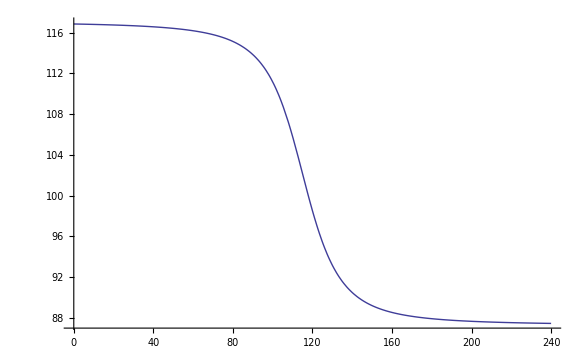

```mathematica
Clear[v0]
```

```mathematica
Plot[D[ft[v0,tp0,l,f0],l],{tp,0,240}]
```